## First we generate all graphs

We will generate an association containing all graphs.  The key of the graph is computed based on a base 4 representation of the upper half of the “adjacency matrix”.
The matrix itself is tri-valued since 0 means no edge, 1 means and edge and 2 mean they are the same vertex.
For each graph we keep

signature  : the "key"
matrix : the "adjancency matrix"
vertexsets : the "sets " of vertices where contracted vertices are in the same set
vertices : th evertices of the graph
edges : the edges of the graph
graph : a picture of the graph

```mathematica
baseGraphs4=GenAll[4];Length[baseGraphs4]
```

127

## Now we calculate the relations

We calculate the relations between the graphs.  This is based on the deletion contraction rule.  It links 4 graphs together in a a=b+c relation (or a subtraction)

```mathematica
withRelations4=CompleteRelations[baseGraphs4];Length[withRelations4]
```

127

For each graph we now add

links  : ids of graphs that are  linked to this graph
relations : a set of equations that involve the current graph.  This set can be empty.  The graph can be mentioned in the relations section of another graph

## Impose a colofour value for the 14 base graphs and propagate this to the others

```mathematica
Table[Labeled[withRelations4[k,"graph"],k],{k,Take[Keys[withRelations4],20]}]
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-9,-Graphics-10,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-18,-Graphics-22,-Graphics-26,-Graphics-27,-Graphics-28,-Graphics-30,-Graphics-31,-Graphics-36}

We take a list of graphs as defined in https://en.wikipedia.org/wiki/Bell_number and give them an arbitrary value.

```mathematica
completeGraphs4=Select[Reverse[Keys[withRelations4]],CompleteGraphQ[withRelations4[#,"graph"]]&];Length[completeGraphs4]
```

15

```mathematica
42
```

42

```mathematica
baseGraphAxioma4=Block[{start=0},Table[start++;Symbol["x"<>ToString[k]]->PartitionToSymbol[withRelations4[k,"vertexsets"]],{k,completeGraphs4}]]
```

{x728→v1234,x697→v123x4,x637→v124x3,x608→v12x34,x607→v12x3x4,x473→v134x2,x448→v13x24,x445→v13x2x4,x400→v14x23,x391→v14x2x3,x377→v1x234,x373→v1x23x4,x367→v1x24x3,x365→v1x2x34,x364→v1x2x3x4}

Now we get some lists of variables

```mathematica
allGraphVariables4=Table[Symbol["x"<> ToString[key]],{key,Keys[withRelations4]}];Length[allGraphVariables4]
```

127

```mathematica
baseGraphAxioma4Vars=Sort[DeleteDuplicates[Flatten[Map[getAllVariables[#[[2]]]&,baseGraphAxioma4]]]];Length[baseGraphAxioma4Vars]
```

15

```mathematica
baseKeys4=Map[SymbolToKey[#[[1]]]&,baseGraphAxioma4]
```

{728,697,637,608,607,473,448,445,400,391,377,373,367,365,364}

```mathematica
Table[Labeled[withRelations4[k,"graph"],k],{k,baseKeys4}]
```

{-Graphics-728,-Graphics-697,-Graphics-637,-Graphics-608,-Graphics-607,-Graphics-473,-Graphics-448,-Graphics-445,-Graphics-400,-Graphics-391,-Graphics-377,-Graphics-373,-Graphics-367,-Graphics-365,-Graphics-364}

```mathematica
Take[baseGraphAxioma4Vars,4]
```

{v1234,v123x4,v124x3,v12x34}

We now take all relations.  Then we combined this with the base graph axioms.  This gives a huge expression list of 7407 equations

We are now in a position to assign the first colofour to each graph:

```mathematica
Monitor[Table[
withRelations4[key]["colofour"]=Simplify[Symbol["x"<>ToString[key]]/.baseGraphAxioma4],
{key,baseKeys4}
],key];
```

## Calculate the colortables

First we create the colortables, inventing variables on the fly if we need them.  Then we solve these variables and discover that once again we can get away with only the 42 base variables.
This procedure only works fior the b01... variables since we need 4 vertices for the current implementation

```mathematica
withColorTables4=withRelations4;
```

```mathematica
Length[Keys[withRelations4]]
```

127

First assign a basic colortable to each base graph

```mathematica
baseGraphKeys4=baseKeys4;
```

```mathematica
baseGraphAxioma4Vars
```

{v1234,v123x4,v124x3,v12x34,v12x3x4,v134x2,v13x24,v13x2x4,v14x23,v14x2x3,v1x234,v1x23x4,v1x24x3,v1x2x34,v1x2x3x4}

```mathematica
Monitor[Table[
withColorTables4[k]["colortable"]=GenerateColorTable4[withColorTables4,k]
,
{k,baseGraphKeys4}
],k];
```

```mathematica
Keys[withColorTables4[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links}

```mathematica
NoPrint[p__]:=TrueQ
```

Now we assign the other colortables by making sure their colofour formula is interpreted with the based color tables

```mathematica
TryComputeColourTable4[k_]:=Block[{result=Null,simp,left,r1,r2, done,current},
current=withColorTables4[k];
If[KeyExistsQ[current,"colortable"],
result=withColorTables4[k,"colortable"],
done=False;
Table[
If[!done,
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
If[!KeyExistsQ[withColorTables4[r1],"colortable"],
withColorTables4[r1,"colortable"]=TryComputeColourTable4[r1],
];
If[!KeyExistsQ[withColorTables4[r2],"colortable"],
withColorTables4[r2,"colortable"]=TryComputeColourTable4[r2],

];
withColorTables4[k,"colortable"]=withColorTables4[r1,"colortable"]+withColorTables4[r2,"colortable"];
withColorTables4[k,"colofour"]=withColorTables4[r1,"colofour"]+withColorTables4[r2,"colofour"];
done=False
];
],
]
,{r,withColorTables4[k]["relations"]}
]
];
withColorTables4[k,"colortable"]
]
```

```mathematica
KeyExistsQ[withColorTables4[0],"colortable"]
```

False

```mathematica
TryComputeColourTable4[0]
```

{{v1234+v123x4+v124x3+v12x34+v12x3x4,v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v123x4+v134x2+v13x24+v13x2x4,v124x3+v12x34+v12x3x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v124x3+v134x2+v14x23+v14x2x3,v123x4+v12x34+v12x3x4+v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v123x4+v14x23+v1x234+v1x23x4,v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v124x3+v13x24+v1x234+v1x24x3,v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4},{v1234+v12x34+v134x2+v1x234+v1x2x34,v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4}}

Now collect all relation equations.  There are quite a few of them.

0

```mathematica
Monitor[Table[
withColorTables4[k]["colortable2"]=withColorTables4[k]["colortable"]
,
{k,Keys[withColorTables4]}
],k];
```

## Set “comp” and “compwhy” for graphs that can be embedded and are planar

```mathematica
withComp4=withColorTables4;
```

Start will all graphs GreaterEqual

```mathematica
Table[withComp4[k,"comp"]=GreaterEqual;withComp4[k,"comp"]="No IH";k,{k,Keys[withComp4]}]//Length
```

127

```mathematica
1894
```

1894

If a base graph is not planar by itself then the  "comp" should be Equal

```mathematica
Table[withComp4[k,"comp"]=Equal;withRelations4[k,"comp"]="Contains K4";k,{k,Select[baseKeys4,!PlanarGraphQ[withComp4[#,"graph"]]&]}]//Length
```

0

```mathematica
Monitor[Table[If[
MyPlanar[withComp4,k],
withComp4[k,"comp"]=Greater;
withComp4[k,"compwhy"]="Planar contraction";
Print[k, " becomes Greater"];
1,
0]
,{k,Keys[withComp4]}],k]
```

0 becomes Greater

1 becomes Greater

2 becomes Greater

3 becomes Greater

4 becomes Greater

6 becomes Greater

9 becomes Greater

10 becomes Greater

12 becomes Greater

13 becomes Greater

14 becomes Greater

16 becomes Greater

18 becomes Greater

22 becomes Greater

26 becomes Greater

27 becomes Greater

28 becomes Greater

30 becomes Greater

31 becomes Greater

36 becomes Greater

37 becomes Greater

39 becomes Greater

40 becomes Greater

45 becomes Greater

49 becomes Greater

54 becomes Greater

63 becomes Greater

72 becomes Greater

81 becomes Greater

82 becomes Greater

90 becomes Greater

91 becomes Greater

108 becomes Greater

109 becomes Greater

110 becomes Greater

117 becomes Greater

118 becomes Greater

122 becomes Greater

136 becomes Greater

145 becomes Greater

162 becomes Greater

190 becomes Greater

218 becomes Greater

243 becomes Greater

244 becomes Greater

245 becomes Greater

246 becomes Greater

247 becomes Greater

252 becomes Greater

253 becomes Greater

255 becomes Greater

256 becomes Greater

257 becomes Greater

270 becomes Greater

271 becomes Greater

273 becomes Greater

274 becomes Greater

276 becomes Greater

279 becomes Greater

280 becomes Greater

282 becomes Greater

283 becomes Greater

286 becomes Greater

300 becomes Greater

309 becomes Greater

324 becomes Greater

325 becomes Greater

333 becomes Greater

334 becomes Greater

342 becomes Greater

346 becomes Greater

351 becomes Greater

352 becomes Greater

353 becomes Greater

360 becomes Greater

361 becomes Greater

365 becomes Greater

369 becomes Greater

373 becomes Greater

377 becomes Greater

382 becomes Greater

391 becomes Greater

400 becomes Greater

414 becomes Greater

442 becomes Greater

473 becomes Greater

486 becomes Greater

487 becomes Greater

488 becomes Greater

516 becomes Greater

517 becomes Greater

546 becomes Greater

576 becomes Greater

577 becomes Greater

606 becomes Greater

607 becomes Greater

608 becomes Greater

637 becomes Greater

666 becomes Greater

697 becomes Greater

728 becomes Greater

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,1,0,0,0,1,1,1,0,0,1,1,0,0,1,1,1,1,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,1,0,0,1,1,1,1,1,0,0,0,1,1,0,0,1,0,1,1,1,1,1,1,1,0,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

## I am certainly not sure about K4

```mathematica
MayBeReassign[key_,current_,left_,right_]:=Block[
{currentS=ToString[current],
leftS=ToString[left],
rightS=ToString[right], result=current},
If[currentS=="GreaterEqual",
If[leftS=="Greater"||rightS=="Greater",
result=Greater;
Print["Changing ", key, " to ",result],
]
];
result
]
```

```mathematica
RecalculateComp4[k_,depth_,maxdepth_]:=Block[{result=Null,simp,left,r1,r2, current},
current=withComp4[k];
If[depth<maxdepth && ! current["marked"],
withComp4[k,"marked"]=True;
markCount++;
Table[
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
RecalculateComp4[r1,depth+1,maxdepth];
withComp4[r1,"parents"]=Append[withComp4[r1,"parents"],k];
RecalculateComp4[r2,depth+1,maxdepth];
withComp4[r2,"parents"]=Append[withComp4[r2,"parents"],k];
withComp4[k,"children"]=Append[withComp4[k,"children"],{r1,r2}];
withComp4[k,"comp"]= MayBeReassign[k,withComp4[k,"comp"], withComp4[r1,"comp"],withComp4[r2,"comp"]]
];
]
,{r,withComp4[k]["relations"]}
];
];withComp4[k,"comp"]
]
```

```mathematica
Table[withComp4[k,"marked"]=False;withComp4[k,"parents"]={};withComp4[k,"children"]={};k,{k,Keys[withComp4]}];markCount=0
```

0

```mathematica
Table[withComp4[k,"comp"]=Equal;withRelations4[k,"comp"]="Contains K4";k,{k,Select[baseKeys4,!PlanarGraphQ[withComp4[#,"graph"]]&]}]//Length
```

0

```mathematica
Monitor[RecalculateComp4[0,0,20],markCount]
```

Greater

```mathematica
Keys[withComp4[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,compwhy,marked,parents,children}

```mathematica
withComp4[1,"children"]
```

{{244,487},{190,82},{136,28},{10,22},{16,4}}

```mathematica
{{19684,39367},{13123,6462},{2188,4104},{3646,730},{244,487},{190,82},{136,28},{10,22},{16,4}}
```

{{19684,39367},{13123,6462},{2188,4104},{3646,730},{244,487},{190,82},{136,28},{10,22},{16,4}}

```mathematica
Select[Keys[withComp4],withComp4[#,"comp"]==GreaterEqual&]//Length
```

0

```mathematica
CosyPrint4[key_]:=With[
{current=withComp4[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{100,100}]
}
],Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current["colofour"]],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},First[Select[{{"Equal",Blue},{"GreaterEqual",Red},{"Greater",Darker[Green]}},#[[1]]==ToString[current["comp"]]&]]]]]
]
```

```mathematica
withComp4[697]
```

<|signature→697,matrix→{{2,2,2,1},{2,2,2,1},{2,2,2,1},{1,1,1,2}},graph→-Graphics-,vertexsets→{{4},{1,2,3}},vertices→{1,2},edges→{{1,2}},relations→{x697==x666-x728},links→{},colofour→v123x4,colortable→{{v123x4,0},{v123x4,0},{0,v123x4},{v123x4,0},{0,v123x4},{0,v123x4}},colortable2→{{v123x4,0},{v123x4,0},{0,v123x4},{v123x4,0},{0,v123x4},{0,v123x4}},comp→Greater,compwhy→Planar contraction,marked→True,parents→{487,517,666,516,165,193,190,45,49,22},children→{}|>

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

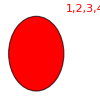
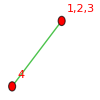
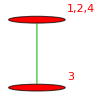
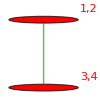
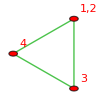
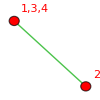
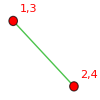
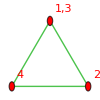
{-Graphics-{728→v1234,1/6},-Graphics-{697→v123x4,1/2},-Graphics-{637→v124x3,1/2},-Graphics-{608→v12x34,1/2},-Graphics-{607→v12x3x4,1},-Graphics-{473→v134x2,1/2},-Graphics-Style[{448→v13x24,1/2},First[{}]],-Graphics-Style[{445→v13x2x4,1},First[{}]],-Graphics-{400→v14x23,1/2},-Graphics-{391→v14x2x3,1},-Graphics-{377→v1x234,1/2},-Graphics-{373→v1x23x4,1},-Graphics-Style[{367→v1x24x3,1},First[{}]],-Graphics-{365→v1x2x34,1},-Graphics-Style[{364→v1x2x3x4,1},First[{}]]}

```mathematica
Table[CosyPrint4[k],{k,baseKeys4}]
```

## We now replace some of the "b" variables with our greek letters

```mathematica
stubbornForm4=withComp4;
```

```mathematica
Keys[stubbornForm4[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,compwhy,marked,parents,children}

```mathematica
CosyPrintThree4[key_]:=ColorTablePrint[key,stubbornForm4,"colofour","colortable2"]
```

```mathematica
stubbornKeys4=Select[Keys[stubbornForm4],stubbornForm4[#,"comp"]==GreaterEqual&];
```

```mathematica
Length[stubbornKeys4]
```

0

```mathematica
Table[CosyPrint4[k],{k,Intersection[baseKeys4,stubbornKeys4]}]
```

{}

```mathematica
stubbornForm4[448,"parents"]
```

{414,442,286,276,168,190,16}

```mathematica
Table[Table[k->p,{p,Select[Flatten[stubbornForm4[k,"parents"]],MemberQ[stubbornKeys4,#]&]}],{k,stubbornKeys4}]
```

{}

```mathematica
stubbornForm4[280,"colofour"]*2-(stubbornForm4[283,"colofour"]+stubbornForm4[361,"colofour"])//Simplify
```

2 v13x24+v13x2x4+v1x24x3

```mathematica
Graph[DeleteDuplicates[Table[
Join[Table[p->k,{p,Select[Flatten[stubbornForm4[k,"parents"]],MemberQ[stubbornKeys4,#]&]}],Table[k->p,{p,Select[Flatten[stubbornForm4[k,"children"]],MemberQ[stubbornKeys4,#]&]}]]
,{k,stubbornKeys4}]//Flatten],VertexLabels->Table[k->CosyPrint4[k],{k,stubbornKeys4}],ImageSize->1000]
```

-Graphics-

```mathematica
Table [Labeled[stubbornForm4[k2,"graph"],stubbornForm4[k2,"colofour"]],{k2,stubbornKeys4}]
```

{}

```mathematica
Table [Labeled[stubbornForm4[k2,"graph"],stubbornForm4[k2,"colofour"]],{k2,baseGraphKeys4}]
```

{-Graphics-v1234,-Graphics-v123x4,-Graphics-v124x3,-Graphics-v12x34,-Graphics-v12x3x4,-Graphics-v134x2,-Graphics-v13x24,-Graphics-v13x2x4,-Graphics-v14x23,-Graphics-v14x2x3,-Graphics-v1x234,-Graphics-v1x23x4,-Graphics-v1x24x3,-Graphics-v1x2x34,-Graphics-v1x2x3x4}

```mathematica
ineqsthree4=Table[stubbornForm4[k]["comp"][stubbornForm4[k]["colofour"],0],{k,Keys[stubbornForm4]}]//Simplify;
```

```mathematica
Take[ineqsthree4,4]
```

{v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0,v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0,v1234+v12x34+v134x2+v1x234+v1x2x34>0,v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4>0}

```mathematica
ineqsthree42=Simplify[Fold[And,ineqsthree4]];Length[ineqsthree42]
```

127

```mathematica
ExpressionToTable2[ineqsthree42]
```

SymbolName::sym: Argument 0 at position 1 is expected to be a symbol.

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[0],1].

SymbolName::sym: Argument 0 at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[0],1].

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[0],1],3,0].

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[0],1],3,0] is not a list of digits or a string of valid digits.

SymbolName::sym: Argument v1234+v13x24 at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[v1234+v13x24],1].

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[0],1].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[v1234+v13x24],1].

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[v1234+v13x24],1],3,0].

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[v1234+v13x24],1],3,0] is not a list of digits or a string of valid digits.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[0],1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[0],1],3,0].

General::stop: Further output of StringPadLeft::strse will be suppressed during this calculation.

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[0],1],3,0] is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[No IH[vx24,0000]].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

v1x234>0
v1234>0
v14x2x3>0
v1x23x4>0
v12x3x4>0
v123x4>0
v134x2>0
v124x3>0
v14x23>0
v1x2x34>0
v12x34>0
v1234+v1x234>0
v1x234+v1x23x4>0
v1234+v123x4>0
v1234+v134x2>0
v1234+v124x3>0
v1234+v14x23>0
v1x234+v1x2x34>0
v1234+v12x34>0
v134x2+v14x2x3>0
v124x3+v14x2x3>0
v14x23+v14x2x3>0
v13x2x4+v1x2x3x4>0
v13x24+v13x2x4>0
v123x4+v1x23x4>0
v123x4+v12x3x4>0
v1x24x3+v1x2x3x4>0
v124x3+v12x3x4>0
v14x23+v1x23x4>0
v12x34+v12x3x4>0
v134x2+v1x2x34>0
v13x24+v1x24x3>0
v12x34+v1x2x34>0
No IH[v123x4+v134x2+v13x2x4,0]
No IH[v134x2+v13x2x4,0]
No IH[v123x4+v13x2x4,0]
No IH[v13x2x4,0]
No IH[v12x34+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4,0]
No IH[v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4,0]
No IH[v12x34+v12x3x4+v1x23x4+v1x2x34+v1x2x3x4,0]
No IH[v1x23x4+v1x2x34+v1x2x3x4,0]
No IH[v12x34+v12x3x4+v14x2x3+v1x2x34+v1x2x3x4,0]
No IH[v14x2x3+v1x2x34+v1x2x3x4,0]
No IH[v12x34+v12x3x4+v1x2x34+v1x2x3x4,0]
No IH[v1x2x34+v1x2x3x4,0]
No IH[v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4,0]
No IH[v14x23+v14x2x3+v1x23x4+v1x2x3x4,0]
No IH[v12x3x4+v1x23x4+v1x2x3x4,0]
No IH[v1x23x4+v1x2x3x4,0]
No IH[v12x3x4+v14x2x3+v1x2x3x4,0]
No IH[v14x2x3+v1x2x3x4,0]
No IH[v12x3x4+v1x2x3x4,0]
No IH[v1x2x3x4,0]
No IH[v124x3+v1x234+v1x24x3,0]
No IH[v1x234+v1x24x3,0]
No IH[v124x3+v1x24x3,0]
No IH[v1x24x3,0]
No IH[v1234+v13x24,0]
No IH[v13x24,0]
v123x4+v1x234+v1x23x4>0
v14x23+v1x234+v1x23x4>0
v134x2+v1x234+v1x2x34>0
v13x24+v1x234+v1x24x3>0
v12x34+v1x234+v1x2x34>0
v13x2x4+v14x2x3+v1x2x3x4>0
v14x2x3+v1x24x3+v1x2x3x4>0
v124x3+v134x2+v14x2x3>0
v134x2+v14x23+v14x2x3>0
v124x3+v14x23+v14x2x3>0
v13x2x4+v1x23x4+v1x2x3x4>0
v12x3x4+v13x2x4+v1x2x3x4>0
v123x4+v13x24+v13x2x4>0
v13x2x4+v1x2x34+v1x2x3x4>0
v134x2+v13x24+v13x2x4>0
v1x23x4+v1x24x3+v1x2x3x4>0
v12x3x4+v1x24x3+v1x2x3x4>0
v123x4+v124x3+v12x3x4>0
v123x4+v14x23+v1x23x4>0
v123x4+v12x34+v12x3x4>0
v1x24x3+v1x2x34+v1x2x3x4>0
v124x3+v12x34+v12x3x4>0
v12x34+v134x2+v1x2x34>0
v124x3+v13x24+v1x24x3>0
v12x3x4+v13x2x4+v14x2x3+v1x2x3x4>0
v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0
v13x2x4+v1x23x4+v1x2x34+v1x2x3x4>0
v13x24+v13x2x4+v1x24x3+v1x2x3x4>0
v12x3x4+v1x23x4+v1x24x3+v1x2x3x4>0
v1234+v123x4+v14x23+v1x234+v1x23x4>0
v1234+v12x34+v134x2+v1x234+v1x2x34>0
v1234+v124x3+v13x24+v1x234+v1x24x3>0
v1234+v124x3+v134x2+v14x23+v14x2x3>0
v1234+v123x4+v134x2+v13x24+v13x2x4>0
v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v1234+v123x4+v124x3+v12x34+v12x3x4>0
v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4>0
v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4>0
v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4>0
v124x3+v12x3x4+v14x2x3+v1x24x3+v1x2x3x4>0
v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0
v123x4+v12x3x4+v13x2x4+v1x23x4+v1x2x3x4>0
v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4>0
v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x3x4>0
v12x34+v12x3x4+v13x2x4+v1x2x34+v1x2x3x4>0
v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4>0
v12x34+v12x3x4+v1x24x3+v1x2x34+v1x2x3x4>0
v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v12x34+v12x3x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v123x4+v12x3x4+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4>0
v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4>0
v12x34+v12x3x4+v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4>0
v124x3+v12x3x4+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4>0
v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0
v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0
v124x3+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0
v124x3+v12x34+v12x3x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0
v123x4+v12x3x4+v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4>0
v123x4+v12x34+v12x3x4+v13x2x4+v1x23x4+v1x2x34+v1x2x3x4>0
v12x34+v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4>0
v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v124x3+v12x34+v12x3x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v123x4+v12x34+v12x3x4+v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4>0
v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0
v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0
v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0

```mathematica
graphicsthree=Map[stubbornForm4[#,"colofour"]->stubbornForm4[#,"graph"]&,Select[Keys[stubbornForm4],Length[ListofVars[stubbornForm4[#,"colofour"]]]==1&]];graphicsthree
```

{v1x2x3x4→-Graphics-,v1x2x34→-Graphics-,v1x24x3→-Graphics-,v1x23x4→-Graphics-,v1x234→-Graphics-,v14x2x3→-Graphics-,v14x23→-Graphics-,v13x2x4→-Graphics-,v13x24→-Graphics-,v134x2→-Graphics-,v12x3x4→-Graphics-,v12x34→-Graphics-,v124x3→-Graphics-,v123x4→-Graphics-,v1234→-Graphics-}

```mathematica
graphicsthree2=Map[stubbornForm4[#,"colofour"]->stubbornForm4[#,"graph"]&,Keys[stubbornForm4]];
```

```mathematica
ExpressionToTable2[ineqsthree42]
```

SymbolName::sym: Argument 0 at position 1 is expected to be a symbol.

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[0],1].

SymbolName::sym: Argument 0 at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[0],1].

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[0],1],3,0].

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[0],1],3,0] is not a list of digits or a string of valid digits.

SymbolName::sym: Argument v1234+v13x24 at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[v1234+v13x24],1].

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[0],1].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[v1234+v13x24],1].

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[v1234+v13x24],1],3,0].

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[v1234+v13x24],1],3,0] is not a list of digits or a string of valid digits.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[0],1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[0],1],3,0].

General::stop: Further output of StringPadLeft::strse will be suppressed during this calculation.

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[0],1],3,0] is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[No IH[vx24,0000]].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

v1x234>0
v1234>0
v14x2x3>0
v1x23x4>0
v12x3x4>0
v123x4>0
v134x2>0
v124x3>0
v14x23>0
v1x2x34>0
v12x34>0
v1234+v1x234>0
v1x234+v1x23x4>0
v1234+v123x4>0
v1234+v134x2>0
v1234+v124x3>0
v1234+v14x23>0
v1x234+v1x2x34>0
v1234+v12x34>0
v134x2+v14x2x3>0
v124x3+v14x2x3>0
v14x23+v14x2x3>0
v13x2x4+v1x2x3x4>0
v13x24+v13x2x4>0
v123x4+v1x23x4>0
v123x4+v12x3x4>0
v1x24x3+v1x2x3x4>0
v124x3+v12x3x4>0
v14x23+v1x23x4>0
v12x34+v12x3x4>0
v134x2+v1x2x34>0
v13x24+v1x24x3>0
v12x34+v1x2x34>0
No IH[v123x4+v134x2+v13x2x4,0]
No IH[v134x2+v13x2x4,0]
No IH[v123x4+v13x2x4,0]
No IH[v13x2x4,0]
No IH[v12x34+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4,0]
No IH[v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4,0]
No IH[v12x34+v12x3x4+v1x23x4+v1x2x34+v1x2x3x4,0]
No IH[v1x23x4+v1x2x34+v1x2x3x4,0]
No IH[v12x34+v12x3x4+v14x2x3+v1x2x34+v1x2x3x4,0]
No IH[v14x2x3+v1x2x34+v1x2x3x4,0]
No IH[v12x34+v12x3x4+v1x2x34+v1x2x3x4,0]
No IH[v1x2x34+v1x2x3x4,0]
No IH[v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4,0]
No IH[v14x23+v14x2x3+v1x23x4+v1x2x3x4,0]
No IH[v12x3x4+v1x23x4+v1x2x3x4,0]
No IH[v1x23x4+v1x2x3x4,0]
No IH[v12x3x4+v14x2x3+v1x2x3x4,0]
No IH[v14x2x3+v1x2x3x4,0]
No IH[v12x3x4+v1x2x3x4,0]
No IH[v1x2x3x4,0]
No IH[v124x3+v1x234+v1x24x3,0]
No IH[v1x234+v1x24x3,0]
No IH[v124x3+v1x24x3,0]
No IH[v1x24x3,0]
No IH[v1234+v13x24,0]
No IH[v13x24,0]
v123x4+v1x234+v1x23x4>0
v14x23+v1x234+v1x23x4>0
v134x2+v1x234+v1x2x34>0
v13x24+v1x234+v1x24x3>0
v12x34+v1x234+v1x2x34>0
v13x2x4+v14x2x3+v1x2x3x4>0
v14x2x3+v1x24x3+v1x2x3x4>0
v124x3+v134x2+v14x2x3>0
v134x2+v14x23+v14x2x3>0
v124x3+v14x23+v14x2x3>0
v13x2x4+v1x23x4+v1x2x3x4>0
v12x3x4+v13x2x4+v1x2x3x4>0
v123x4+v13x24+v13x2x4>0
v13x2x4+v1x2x34+v1x2x3x4>0
v134x2+v13x24+v13x2x4>0
v1x23x4+v1x24x3+v1x2x3x4>0
v12x3x4+v1x24x3+v1x2x3x4>0
v123x4+v124x3+v12x3x4>0
v123x4+v14x23+v1x23x4>0
v123x4+v12x34+v12x3x4>0
v1x24x3+v1x2x34+v1x2x3x4>0
v124x3+v12x34+v12x3x4>0
v12x34+v134x2+v1x2x34>0
v124x3+v13x24+v1x24x3>0
v12x3x4+v13x2x4+v14x2x3+v1x2x3x4>0
v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0
v13x2x4+v1x23x4+v1x2x34+v1x2x3x4>0
v13x24+v13x2x4+v1x24x3+v1x2x3x4>0
v12x3x4+v1x23x4+v1x24x3+v1x2x3x4>0
v1234+v123x4+v14x23+v1x234+v1x23x4>0
v1234+v12x34+v134x2+v1x234+v1x2x34>0
v1234+v124x3+v13x24+v1x234+v1x24x3>0
v1234+v124x3+v134x2+v14x23+v14x2x3>0
v1234+v123x4+v134x2+v13x24+v13x2x4>0
v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v1234+v123x4+v124x3+v12x34+v12x3x4>0
v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4>0
v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4>0
v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4>0
v124x3+v12x3x4+v14x2x3+v1x24x3+v1x2x3x4>0
v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0
v123x4+v12x3x4+v13x2x4+v1x23x4+v1x2x3x4>0
v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4>0
v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x3x4>0
v12x34+v12x3x4+v13x2x4+v1x2x34+v1x2x3x4>0
v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4>0
v12x34+v12x3x4+v1x24x3+v1x2x34+v1x2x3x4>0
v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v12x34+v12x3x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v123x4+v12x3x4+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4>0
v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4>0
v12x34+v12x3x4+v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4>0
v124x3+v12x3x4+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4>0
v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0
v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0
v124x3+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0
v124x3+v12x34+v12x3x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0
v123x4+v12x3x4+v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4>0
v123x4+v12x34+v12x3x4+v13x2x4+v1x23x4+v1x2x34+v1x2x3x4>0
v12x34+v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4>0
v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v124x3+v12x34+v12x3x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v123x4+v12x34+v12x3x4+v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0
v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4>0
v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0
v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0
v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0

## Now define full

```mathematica
fiveNodes=withComp4;
```

```mathematica
DefineFull4[]:=Block[{empty = fiveNodes[lambdaKey4],amigo1=fiveNodes[alfaKey4], amigo2=fiveNodes[betaKey4], newEntry, fivePositions},
fivePositions=Append[N[MyCircle[{{1},{2},{3},{4}},4]],{0,0}];
newEntry=Association[];
newEntry["signature"]="full";
Table[
newEntry[key]=Simplify[2*empty[key]-(amigo1[key]+amigo2[key])]
,{key,{"colofour","colortable"}}
];
newEntry["comp"]=GreaterEqual;
newEntry["compwhy"]="This is to be proven";
newEntry["matrix"]=empty["matrix"];
newEntry["graph"]=Graph[{1<->2,2<->3,3<->4,4<->1,5<->1,5<->2,5<->3,5<->4},VertexLabels->"Name",VertexSize->Normal,
ImageSize->{50,50},VertexCoordinates->fivePositions];
newEntry["vertexsets"]=empty["vertexsets"];
newEntry["vertices"]=empty["vertices"];
newEntry["relations"]={};
newEntry
]
```

```mathematica
fiveNodes["full"]=DefineFull4[];
```

```mathematica
ColorTablePrint["full",fiveNodes,"colofour","colortable"]/.graphicsthree
```

-Graphics-full2 -Graphics-+-Graphics-+-Graphics-GreaterEqual
( | = | ≠
1<->2 | 0 | 2 -Graphics-+-Graphics-+-Graphics-
1<->3 | 2 -Graphics-+-Graphics- | -Graphics-
1<->4 | 0 | 2 -Graphics-+-Graphics-+-Graphics-
2<->3 | 0 | 2 -Graphics-+-Graphics-+-Graphics-
2<->4 | 2 -Graphics-+-Graphics- | -Graphics-
3<->4 | 0 | 2 -Graphics-+-Graphics-+-Graphics-)

## For all we have not nailed yet, we set their colofour to zero and combine them with the inequalities

```mathematica
ineqsthree42
```

v1234+v123x4+v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0&&v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0&&v1234+v12x34+v134x2+v1x234+v1x2x34>0&&v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4>0&&v123x4+v12x3x4+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4>0&&v1234+v124x3+v13x24+v1x234+v1x24x3>0&&v124x3+v12x34+v12x3x4+v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0&&v124x3+v12x3x4+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4>0&&v12x34+v12x3x4+v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4>0&&v12x3x4+v13x2x4+v14x2x3+v1x2x3x4>0&&v12x34+v134x2+v1x2x34>0&&v124x3+v13x24+v1x24x3>0&&v1234+v123x4+v14x23+v1x234+v1x23x4>0&&v123x4+v14x23+v1x23x4>0&&v1234+v1x234>0&&v123x4+v12x34+v12x3x4+v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0&&v123x4+v12x3x4+v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4>0&&v123x4+v12x34+v12x3x4+v13x2x4+v1x23x4+v1x2x34+v1x2x3x4>0&&v123x4+v12x3x4+v13x2x4+v1x23x4+v1x2x3x4>0&&v12x34+v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4>0&&v12x3x4+v13x24+v13x2x4+v1x24x3+v1x2x3x4>0&&v12x34+v12x3x4+v13x2x4+v1x2x34+v1x2x3x4>0&&v12x3x4+v13x2x4+v1x2x3x4>0&&v123x4+v1x234+v1x23x4>0&&v123x4+v1x23x4>0&&v1234+v124x3+v134x2+v14x23+v14x2x3>0&&v124x3+v134x2+v14x2x3>0&&v1234+v14x23>0&&v124x3+v12x34+v12x3x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0&&v124x3+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0&&No IH[v12x34+v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4,0]&&No IH[v12x3x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4,0]&&No IH[v124x3+v1x234+v1x24x3,0]&&v124x3+v12x34+v12x3x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0&&v124x3+v12x3x4+v14x2x3+v1x24x3+v1x2x3x4>0&&No IH[v12x34+v12x3x4+v14x2x3+v1x2x34+v1x2x3x4,0]&&No IH[v12x3x4+v14x2x3+v1x2x3x4,0]&&No IH[v124x3+v1x24x3,0]&&v12x34+v12x3x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0&&v12x3x4+v1x23x4+v1x24x3+v1x2x3x4>0&&v12x34+v1x234+v1x2x34>0&&No IH[v12x34+v12x3x4+v1x23x4+v1x2x34+v1x2x3x4,0]&&No IH[v12x3x4+v1x23x4+v1x2x3x4,0]&&v12x34+v12x3x4+v1x24x3+v1x2x34+v1x2x3x4>0&&v12x3x4+v1x24x3+v1x2x3x4>0&&No IH[v12x34+v12x3x4+v1x2x34+v1x2x3x4,0]&&No IH[v12x3x4+v1x2x3x4,0]&&v12x34+v1x2x34>0&&v124x3+v14x23+v14x2x3>0&&v124x3+v14x2x3>0&&v1234+v123x4+v134x2+v13x24+v13x2x4>0&&No IH[v123x4+v134x2+v13x2x4,0]&&No IH[v1234+v13x24,0]&&v123x4+v13x24+v13x2x4>0&&No IH[v123x4+v13x2x4,0]&&v1234+v134x2>0&&v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0&&v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0&&v134x2+v1x234+v1x2x34>0&&v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4>0&&v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x3x4>0&&v134x2+v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0&&v13x24+v13x2x4+v14x2x3+v1x24x3+v1x2x3x4>0&&v134x2+v13x2x4+v14x2x3+v1x2x34+v1x2x3x4>0&&v13x2x4+v14x2x3+v1x2x3x4>0&&v134x2+v1x2x34>0&&v13x24+v13x2x4+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0&&v13x24+v13x2x4+v1x23x4+v1x24x3+v1x2x3x4>0&&v13x2x4+v1x23x4+v1x2x34+v1x2x3x4>0&&v13x2x4+v1x23x4+v1x2x3x4>0&&v13x24+v1x234+v1x24x3>0&&v13x24+v13x2x4+v1x24x3+v1x2x34+v1x2x3x4>0&&v13x24+v13x2x4+v1x24x3+v1x2x3x4>0&&v13x2x4+v1x2x34+v1x2x3x4>0&&v13x2x4+v1x2x3x4>0&&v13x24+v1x24x3>0&&v134x2+v14x23+v14x2x3>0&&v134x2+v14x2x3>0&&v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0&&v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4>0&&No IH[v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4,0]&&No IH[v14x23+v14x2x3+v1x23x4+v1x2x3x4,0]&&v14x2x3+v1x24x3+v1x2x34+v1x2x3x4>0&&v14x2x3+v1x24x3+v1x2x3x4>0&&No IH[v14x2x3+v1x2x34+v1x2x3x4,0]&&No IH[v14x2x3+v1x2x3x4,0]&&v14x23+v1x234+v1x23x4>0&&v14x23+v1x23x4>0&&v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4>0&&v1x23x4+v1x24x3+v1x2x3x4>0&&v1x234+v1x2x34>0&&No IH[v1x23x4+v1x2x34+v1x2x3x4,0]&&No IH[v1x23x4+v1x2x3x4,0]&&No IH[v1x234+v1x24x3,0]&&v1x24x3+v1x2x34+v1x2x3x4>0&&v1x24x3+v1x2x3x4>0&&No IH[v1x2x34+v1x2x3x4,0]&&No IH[v1x2x3x4,0]&&v1x2x34>0&&No IH[v1x24x3,0]&&v1x234+v1x23x4>0&&v1x23x4>0&&v1x234>0&&v14x23+v14x2x3>0&&v14x2x3>0&&v14x23>0&&v134x2+v13x24+v13x2x4>0&&No IH[v134x2+v13x2x4,0]&&v13x24+v13x2x4>0&&No IH[v13x2x4,0]&&No IH[v13x24,0]&&v134x2>0&&v1234+v123x4+v124x3+v12x34+v12x3x4>0&&v123x4+v124x3+v12x3x4>0&&v1234+v12x34>0&&v123x4+v12x34+v12x3x4>0&&v123x4+v12x3x4>0&&v1234+v124x3>0&&v124x3+v12x34+v12x3x4>0&&v124x3+v12x3x4>0&&v12x34+v12x3x4>0&&v12x3x4>0&&v12x34>0&&v124x3>0&&v1234+v123x4>0&&v123x4>0&&v1234>0

```mathematica
TryZeroFor4[key_]:=Block[{current=fiveNodes[key]},
If[ToString[Reduce[current["colofour"]==0&&ineqsthree42]]=="False",
current["comp"]=Greater;
current["compwhy"]="Would be inconsistent with other inequalities";
fiveNodes[key]=current;
Print[key, " becomes Greater because of inequalities"];
1,
0
]
]
```

```mathematica
stillAProblem4=Select[Keys[fiveNodes],ToString[fiveNodes[#,"comp"]]=="GreaterEqual"&];Length[stillAProblem4]
```

1

```mathematica
Table[fiveNodes[k,"graph"],{k,stillAProblem4}]
```

{-Graphics-}

```mathematica
Monitor[Table[TryZeroFor4[k],{k,Select[Keys[treeForm5],!NumberQ[#]&]}],{k}]//Total
```

Reduce::naqs: «1» is not a quantified system of equations and inequalities.

General::stop: Further output of Reduce::naqs will be suppressed during this calculation.

0

```mathematica
TryZeroFor5["full"]
```

0

```mathematica
GetCompTreeForm[key_]:=Block[{},treeForm5[key]]
```

```mathematica
SetCompTreeForm[key_,value_]:=Block[{},treeForm5[key]=value]
```

```mathematica
PropagateComp[GetCompTreeForm,SetCompTreeForm,Keys[treeForm5]]
```

Table::iterb: Iterator {rel,Missing[KeyAbsent,729][relations]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table[1,{rel,Missing[KeyAbsent,729][relations]}]+Table[rel2=Simplify[rel];lhs=rel2⟦1⟧;rhs=rel2⟦2⟧;If[Length[lhs]==0,one=SymbolToKey[lhs];two=SymbolToKey[rhs⟦1⟧];three=SymbolToKey[rhs⟦2⟧];,one=SymbolToKey[rhs];two=SymbolToKey[lhs⟦1⟧];three=SymbolToKey[lhs⟦2⟧]];onecomp=ToString[GetCompTreeForm[one][comp]];twocomp=ToString[GetCompTreeForm[two][comp]];threecomp=ToString[GetCompTreeForm[three][comp]];If[onecomp==GreaterEqual,If[twocomp==Greater||threecomp==Greater,1,0],0],{rel,Missing[KeyAbsent,730][relations]}]+1785+Table[1,1]+Table[1,{rel,Missing[KeyAbsent,full][relations]}]
 |  |  |  |

```mathematica
stillABigProblem5=Select[Keys[treeForm5],ToString[treeForm5[#,"comp"]]=="GreaterEqual"&];Length[stillABigProblem5]
```

201